# Project report

## Aromatics

D Malan

Department of Chemistry
University of Pretoria

02 February 2020

## Introduction

Spiking diesel with some aromatic compounds to see where they elute.

## Experimental

### Base sample

Total™ 50 ppm diesel.

### Aromatics to add

```mathematica
aromatics ={"Cumene", "1,4-diisopropylbenzene","Bibenzyl", "Naphthalene", "Anthracene", "Chrysene", "BenzoApyrene"}
```

{Cumene,1,4-diisopropylbenzene,Bibenzyl,Naphthalene,Anthracene,Chrysene,BenzoApyrene}

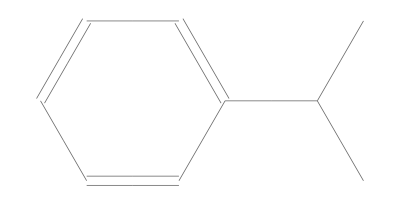
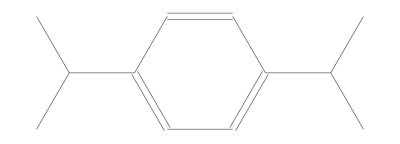
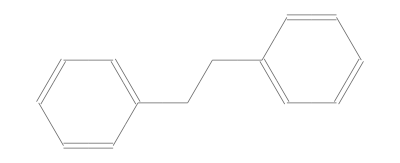
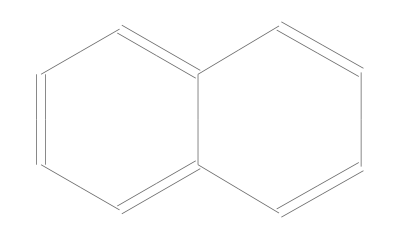
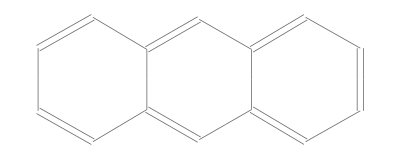
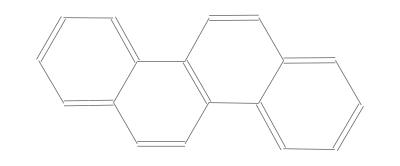
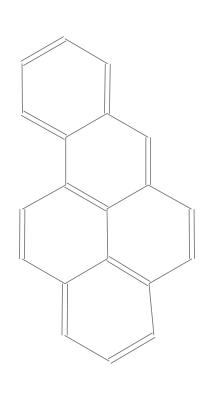
-Graphics- | cumene | 153. °C
-Graphics- | 1,4-diisopropylbenzene | 210. °C
-Graphics- | bibenzyl | 284. °C
-Graphics- | naphthalene | 218. °C
-Graphics- | anthracene | 340. °C
-Graphics- | chrysene | 448. °C
-Graphics- | benzo[a]pyrene | 495. °C

```mathematica
TableForm[{ChemicalData[#], ChemicalData[#, "Name"], ChemicalData[#, "BoilingPoint"]}&/@ aromatics ]
```

### Masses:

```mathematica
mdiesel = 1.3355-0.0536
```

1.2819

```mathematica
maromatics = {0.0536-0.0452, 0.0452-0.0359,0.0359-0.0217,0.0217-0.0134, 0.0134-0.0063, 0.0063-0.0031, 0.0031}
```

{0.0084,0.0093,0.0142,0.0083,0.0071,0.0032,0.0031}

```mathematica
Total[maromatics]
```

0.0536

```mathematica
TableForm[Join[{aromatics},{ maromatics}, {Quantity[maromatics*100/(mdiesel+Total[maromatics]), "Percent"]}]]
```

Cumene | 1,4-diisopropylbenzene | Bibenzyl | Naphthalene | Anthracene | Chrysene | BenzoApyrene
0.0084 | 0.0093 | 0.0142 | 0.0083 | 0.0071 | 0.0032 | 0.0031
0.628978 % | 0.696368 % | 1.06327 % | 0.62149 % | 0.531636 % | 0.239611 % | 0.232123 %

```mathematica
Quantity[Total[maromatics]/(mdiesel+Total[maromatics]), "Percent"]
```

0.0401348 %

## Calculations

### Mixture

I have found that I can weigh about 15 mg of PAH conveniently. Then the total mass of the spikes will be:

```mathematica
spikemass =Length[aromatics]*Quantity[0.015, "Grams"]
```

0.105 g

To make a 10% solution of these spikes, the total mass of the solution will be

```mathematica
totalmass = spikemass × 10
```

1.05 g

```mathematica
dieselmass = totalmass-spikemass
```

0.945 g

In general, I am afraid 10% will be a bit on the high side, so I will just dissolve the aromatics in 1 g of diesel

```mathematica
pahfraction = UnitConvert[ spikemass/(Quantity[2, "Grams"]+spikemass), "Percent"]
```

4.98812 %

## Results

## Discussion

## Conclusion

## Recommendations